# Polarization-Aware Modular IR Apertures for Interference Mitigation in Multi-User Indoor Networks Supplementary Material:Numerical Simulations

## Abstract :A polarization-aware method improves modular clustered IR optical apertures to mitigate inter-user interference in multi-user near-field indoor networks. Assigning orthogonal polarization with aligned receivers enhances SINR and leads to a considerable reduction in average BER, confirming improved reliability. Copyright © 2025 Sharadhi Gunathilake This code accompanies the conference publication: “Polarization-Aware Modular IR Apertures for Interference Mitigation in Multi-User Indoor Networks”, provided for academic and research reference purposes only.

## Initialization and styling

```mathematica
ClearAll["Global`*"](*Clear Variables and memory*)
```

## Numerical Simulations

Dual carrier framework: wavelength choice

```mathematica
plotWithWaveLengthDif[λ2Min_,λ2Max_,res_]:=Module[{λ1,y,temp},
λ1=1560000;(*wave length in picometers*)
y=Table[{λ2-λ1},{λ2,λ2Min,λ2Max,res}];
output=Table[{(λ1*λ2*10^-12)/(λ2-λ1)},{λ2,λ2Min,λ2Max,res}];
temp=Table[MapThread[List,{y[[;;,1]],output[[;;,1]]}]];
ListPlot[temp,Joined->True,FrameTicks->{Table[x,{x,0,12,1}],Table[x,{x,0,3,0.5}]},Frame->{{True,False},{True,False}},AxesOrigin->{0,0},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],FrameLabel->{"λ_d-λ_b(pm)","Maximum Cluster Spacing(m)"},PlotStyle->{{Thickness->Large,Darker[Blue]}},Epilog->{Lighter@Red,Dashed,PointSize[0.01],Thickness[0.01],Line[{{4.868,0},{4.868,0.5},{0,0.5}}]},PlotRangePadding->None,ImageSize->Large]
]
```

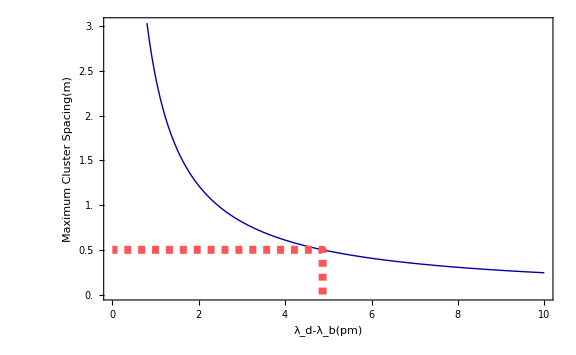

```mathematica
plotWithWaveLengthDif[1560000.001,1560010,0.001]
```

Defining Functional and dimensional parameters

Functional parameters for the dual carrier framework

```mathematica
λd = 1.56*10^-6; (*data wavelength*)
wavelengthDiff =4*1.2*10^-12; 
λb = λd - wavelengthDiff; (*baseline wavelength*)
λe =2*(λd*λb)/(λd - λb);(*effective wavelength*)
```

Dimensional parameters of an indoor room

```mathematica
xLength=3;
yLength=4;
zHeight=3;
xMiddle=Round[xLength]/2;
yMiddle=Round[yLength]/2;
```

Dimensional parameters of optical aperture of IR radiative elements

```mathematica
mx1=6; (*Cluster count along x axis*)
my1=8;(* Cluster count along y axis*)
nx1=6;(*IR elements in a cluster along x axis*)
ny1=6;(*IR elements in a cluster along y axis*)
```

```mathematica
Dis1=0.5;(* Distance between IR clusters is 0.5 m*)
dis1=λd/2;(* Distnace between nano radiating elements is half of the IR wavelength*)
```

Multi beam focusing pattern of the proposed planar optical aperture

Define sub-cluster segmentation algorithm

```mathematica
selectValidSubMatrixDimension[matrixRowCount_,matrixColCount_,subMatrixCount_]:=Module[{totalElems,subMatrixSize,possibleRowDimensions,r,c,validDimensions,mostSquareDimension},
totalElems=matrixRowCount*matrixColCount;
subMatrixSize=totalElems/subMatrixCount;
(*Find possible Row dimensions for the calculated submaitrxSize*)
possibleRowDimensions=Select[Divisors[subMatrixSize],Divisible[matrixRowCount,#]&];
(*find matching Column Size for the Possible Row Dimensions and then select possible couples which can accomadate subMatrix by finindg correct column sizes*)
validDimensions=Select[Table[{r,c=subMatrixSize/r},{r,possibleRowDimensions}],Divisible[matrixColCount,#[[2]]]&];
(*Select MSot squarer pairs and if there are tow select low row count with high col count*)
mostSquareDimension=MinimalBy[validDimensions,Abs[#[[1]]-#[[2]]]&];
(*If[Length[mostSquareDimension]>=1, Return[mostSquareDimension[[1]]],Return[mostSquareDimension]]*);
Return[mostSquareDimension[[1]]];
]
```

```mathematica
subdividingMatrix[uElems_,vElems_,userCount_]:=Module[{factors,nearestFactor,subMatrixDimension,matrix,r,c,u,v,m,n},
factors=Divisors[uElems*vElems];
(*Finding nearest factor for the given number of users*)
nearestFactor=SelectFirst[factors,#>=userCount&];
(*Find the best submatrix dimension for the given number of users*)
subMatrixDimension=selectValidSubMatrixDimension[uElems,vElems,nearestFactor];
subMatrixDimension
]
```

Define the SINR at the user location

```mathematica
sinr[subMatrixDim_,focalPoints_,userFocalPoint_,noiseVar_]:=Module[{elementPoint,nx,ny,mx,my,clusterMidPoint,rt,rp,userIndex,r,c,m,n,assignedSubMatrices,totalField,userField,interferenceField,amp,rpI,deltaArrI,TotalAmp,userBeamAmp,intereferenceAmp,sinrValue},
elementPoint={xMiddle+(dis1/2*(2*nx-nx1-1)+Dis1/2*(2*mx-mx1-1)),yMiddle+(dis1/2*(2*ny-ny1-1)+Dis1/2*(2*my-my1-1)),zHeight};
clusterMidPoint={xMiddle+Dis1/2*(2*mx-mx1-1),yMiddle+Dis1/2*(2*my-my1-1),zHeight};
rt=EuclideanDistance[userFocalPoint,clusterMidPoint];
rp=EuclideanDistance[userFocalPoint,elementPoint];
userIndex=First@Flatten@Position[focalPoints,userFocalPoint];
r=subMatrixDim[[1]];
c=subMatrixDim[[2]];
assignedSubMatrices=1;
userField=0;
interferenceField=0;
For[m=1,m<=nx1,m+=r,{
For[n=1,n<=ny1,n+=c,{
If[assignedSubMatrices>Length[focalPoints],Break[],];
rpI=EuclideanDistance[focalPoints[[assignedSubMatrices]],elementPoint];
deltaArrI=rp-rpI;
amp=∑_(nx=m)^(m+r-1) ∑_(ny=n)^(n+c-1) (Cos[(2π)/λe*deltaArrI]*Exp[-ⅈ*(2π)/λd*deltaArrI])/rt;
If[assignedSubMatrices==userIndex,userField+=amp,interferenceField+=amp];
assignedSubMatrices++;
}]
}];
userBeamAmp=Abs[Total[Table[userField,{mx,1,mx1},{my,1,my1}],2]];
(*Print[userBeamAmp]*);
intereferenceAmp=Abs[Total[Table[interferenceField,{mx,1,mx1},{my,1,my1}],2]];
(*Print[intereferenceAmp]*);
sinrValue=10*Log10[userBeamAmp^2/(intereferenceAmp^2+noiseVar)];
sinrValue
]
```

Define receiver positions in the room

```mathematica
userLocations1={{1.2,1.5,0.75},{2.4,2.5,0.75},{2.5,2.6,0.75},{2.3,1.4,0.75},{2.7,0.5,0.75},{1.4,0.8,0.75}};
(*{{1,1.5,0.75},{3,2.5,0.75},{3,2.6,0.75},{3,1.4,0.75},{2.7,0.5,0.75},{1.4,0.8,0.75}}*)
```

```mathematica
(*Best {{1.2,1.5,0.75},{2.4,2.5,0.75},{2.5,2.6,0.75},{2.3,1.4,0.75},{2.7,0.5,0.75},{1.4,0.8,0.75}}*)
```

```mathematica
subMatrixDim1=subdividingMatrix[nx1,ny1,Length[userLocations1]];
```

SINR calculation for given user locations

```mathematica
sinrCal[userLocations_,subClusterDim_]:=Module[{sinrList={},sinrVal=0},
For[i=1,i<=Length[userLocations],i++,
{
sinrVal=sinr[subClusterDim,userLocations,userLocations[[i]],10];
AppendTo[sinrList,sinrVal];
}
];
sinrList
]
```

```mathematica
sinrWithoutPolList=sinrCal[userLocations1,subMatrixDim1]
```

{12.2288,21.5682,21.084,15.3002,23.2285,17.3118}

Introduce Polarization effect at both transmitter and receiver

Polarization Assignment resulting better SINR at receiver locations

Define the SINR at the user location with polarization

```mathematica
getPolVec[modulePositions_,receieverQ_,pVec_]:=Module[{rHat,Lambda,polVec},
rHat=Normalize[receieverQ-modulePositions];
Lambda=IdentityMatrix[3]-Outer[Times,rHat,rHat];
polVec=Lambda.pVec;
polVec
]
```

```mathematica
sinrPol[subMatrixDim_,focalPoints_,userFocalPoint_,polVectorList_,noiseVar_]:=Module[{elementPoint,nx,ny,mx,my,clusterMidPoint,rt,rp,userIndex,r,c,m,n,assignedSubMatrices,polVec,detectVec,propagatedPolVec,proj,totalField,userField,interferenceField,amp,rpI,deltaArrI,TotalAmp,userBeamAmp,intereferenceAmp,sinr},
elementPoint={xMiddle+(dis1/2*(2*nx-nx1-1)+Dis1/2*(2*mx-mx1-1)),yMiddle+(dis1/2*(2*ny-ny1-1)+Dis1/2*(2*my-my1-1)),zHeight};
clusterMidPoint={xMiddle+Dis1/2*(2*mx-mx1-1),yMiddle+Dis1/2*(2*my-my1-1),zHeight};
rt=EuclideanDistance[userFocalPoint,clusterMidPoint];
rp=EuclideanDistance[userFocalPoint,elementPoint];
userIndex=First@Flatten@Position[focalPoints,userFocalPoint];
r=subMatrixDim[[1]];
c=subMatrixDim[[2]];
assignedSubMatrices=1;
userField=0;
interferenceField=0;
detectVec=polVectorList[[userIndex]];
For[m=1,m<=nx1,m+=r,{
For[n=1,n<=ny1,n+=c,{
If[assignedSubMatrices>Length[focalPoints],Break[],];
rpI=EuclideanDistance[focalPoints[[assignedSubMatrices]],elementPoint];
deltaArrI=rp-rpI;
polVec=polVectorList[[assignedSubMatrices]];
propagatedPolVec=getPolVec[clusterMidPoint,userFocalPoint,polVec];
proj=Dot[detectVec,propagatedPolVec];
amp=proj*∑_(nx=m)^(m+r-1) ∑_(ny=n)^(n+c-1) (Cos[(2π)/λe*deltaArrI]*Exp[-ⅈ*(2π)/λd*deltaArrI])/rt;
If[assignedSubMatrices==userIndex,userField+=amp,interferenceField+=amp];
assignedSubMatrices++;
}]
}];
userBeamAmp=Abs[Total[Table[userField,{mx,1,mx1},{my,1,my1}],2]];
(*Print[userBeamAmp]*);
intereferenceAmp=Abs[Total[Table[interferenceField,{mx,1,mx1},{my,1,my1}],2]];
(*Print[intereferenceAmp]*);
sinr=10*Log10[userBeamAmp^2/(intereferenceAmp^2+noiseVar)];
sinr
]
```

Exhaustive Search method

```mathematica
sinrCalPol[userLocations_,sinrWithoutPol_,subClusterDim_]:=Module[{possiblePolList={},totalSinrList,sinrPolList,sinrPolVal,resultList={},polairizationList={},result,index,polarizationConfig},
possiblePolList=Tuples[{{1,0,0},{0,1,0}},Length[userLocations]];
totalSinrList={};
For[i=1,i<=Length[possiblePolList],i++,
{
(*Print[possiblePolList[[i]]];*)
sinrPolList={};
For[j=1,j<=Length[userLocations],j++,
{
sinrPolVal=sinrPol[subClusterDim,userLocations,userLocations[[j]],possiblePolList[[i]],10];
AppendTo[sinrPolList,sinrPolVal];
}
];
(*Print[sinrPolList]*);
AppendTo[totalSinrList,sinrPolList];
If[AllTrue[Thread[sinrPolList>sinrWithoutPol],TrueQ],{(*Print["Found a list where all elements are greater than prior SINR values: ",sinrPolList];*)
AppendTo[polairizationList,possiblePolList[[i]]];
AppendTo[resultList,sinrPolList];
}];
}
];
If[resultList=={},
{
result=First@MaximalBy[totalSinrList,Total];
index=First@FirstPosition[totalSinrList,result];
polarizationConfig=possiblePolList[[index]];
},
{result=First@MaximalBy[resultList,Total];
index=First@FirstPosition[resultList,result];
polarizationConfig=polairizationList[[index]];
}
];
{polarizationConfig,result,Mean[result]}
]
```

```mathematica
sinrWithPolList=sinrCalPol[userLocations1,sinrWithoutPolList,subMatrixDim1]
```

{{{1,0,0},{0,1,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0}},{26.7536,25.7044,25.7142,28.5022,24.0864,26.4933},26.209}

Greedy Search method

```mathematica
(*Introduce horiziontal pol and vertical pol in 3D vector format*)
polFromBit[0]:={1,0,0};
polFromBit[1]:={0,1,0};
```

```mathematica
(*Building detector pol list for Q users*)
makeDetectPolList[labels01_]:=polFromBit/@labels01
```

```mathematica
(*Evaluate selected pol assignment using sinrPol (SINR in DB for that assignment)*)
computeSINRList[labels01_,subClusDim_,userLocations_,noiseVar_]:=Module[{detectorPolList,emitterPolList,sinrPolList={},j},
detectorPolList=makeDetectPolList[labels01];
For[j=1,j<=Length[userLocations],j++,
AppendTo[sinrPolList,sinrPol[subClusDim,userLocations,userLocations[[j]],detectorPolList,noiseVar]]
];
sinrPolList
]
```

```mathematica
(*Find mean SINR(dB), with a hard penalty if any user is worse than unpolarized*)
score[sinrList_,sinrUnPolList_]:=Module[{penalty},
penalty=100*Count[Thread[sinrList>sinrUnPolList],False];
Mean[sinrList]-penalty
]
```

```mathematica
(*Greedy search block for the best SINR*)
greedyHV[subClusDim_,userLocations_,noiseVar_,sinrUnPol_,restartCount_]:=Module[{Q=Length[userLocations],q,r,labels,sinrList,scoreVal,improved,trialLabels,sinrTrial,scoreTrial,bestLabels={},bestSINR=0,bestScore=-Infinity},
Do[
(*define polLabels:for first run we use alternatively, for remaining runs we decide it randomly*)
labels=If[r==1,Table[Mod[i,2],{i,1,Q}],RandomInteger[{0,1},Q]];
(*Print[labels]*);
sinrList=computeSINRList[labels,subClusDim,userLocations,noiseVar];
(*Print[sinrList]*);
scoreVal=score[sinrList,sinrUnPol];

improved=True;
While[improved,
improved=False;
Do[
trialLabels=ReplacePart[labels,q->1-labels[[q]]];(*Flip user q*)
sinrTrial=computeSINRList[trialLabels,subClusDim,userLocations,noiseVar];
scoreTrial=score[sinrTrial,sinrUnPol];
If[scoreTrial>scoreVal,
{labels=trialLabels;
(*Print[labels]*)
sinrList=sinrTrial;
(*Print[sinrList]*)
scoreVal=scoreTrial;
improved=True;},{}];
,{q,1,Q}];
];

If[scoreVal>bestScore,{bestScore=scoreVal;bestLabels=labels;bestSINR=sinrList;},{}]
,{r,1,restartCount}];

{makeDetectPolList[bestLabels],bestSINR,Mean[bestSINR]}
];
```

```mathematica
sinrWithPolListGreedy=greedyHV[subMatrixDim1,userLocations1,10,sinrWithoutPolList,6]
```

{{{1,0,0},{0,1,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0}},{26.7536,25.7044,25.7142,28.5022,24.0864,26.4933},26.209}

```mathematica
userLabels=Table[{i,"R"<>ToString[i]},{i,Length[userLocations1]}];
```

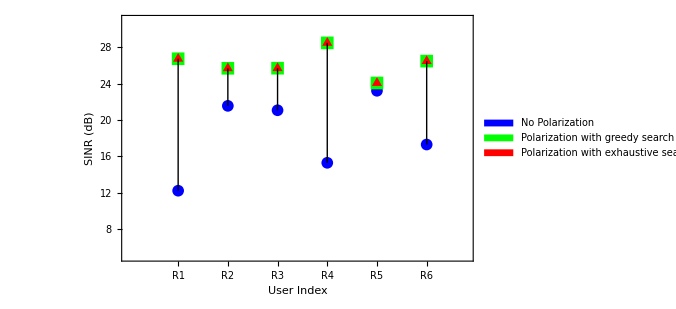

```mathematica
ListLinePlot[{sinrWithoutPolList,sinrWithPolListGreedy[[2]],sinrWithPolList[[2]]},PlotStyle->{Blue,Green,Red},PlotMarkers->{Style["●",12],Style["■",13],Style["▲",12]},Joined->False,PlotLegends->Placed[SwatchLegend[{"No Polarization","Polarization with greedy search","Polarization with exhaustive search"},LabelStyle->{FontFamily->"Times New Roman"}],{0.7,0.2}],PlotRange->{{0,6.8},{5,31}},Epilog->{Table[Line[{{i,sinrWithoutPolList[[i]]},{i,sinrWithPolListGreedy[[2]][[i]]}}],{i,1,Length[sinrWithoutPolList]}]},ImageSize->500,BaseStyle->{FontFamily->"Times New Roman",FontSize->13},Frame->True,FrameLabel->{(*use frame labels instead of axes labels*)Style["User Index",FontFamily->"Times New Roman"],Style["SINR (dB)",FontFamily->"Times New Roman"]},FrameTicks->{{Automatic,Automatic},{userLabels,Automatic}},ImagePadding->{{40,10},{40,10}}]
```

BER calculation

```mathematica
QFunction[x_]:=1/2*Erfc[x/Sqrt[2]];
```

```mathematica
(*Assume SINR list is per-symbol;set perBit->True if your SINR is Eb/(N0+I0)*)berMPAM[sinrDB_List,M_Integer,perBit_:False]:=Module[{gamma=10^(sinrDB/10.),k},k=If[perBit,(6 Log[2,M])/(M^2-1),6/(M^2-1)];
(2 (M-1)/(M Log[2,M]))*QFunction[Sqrt[k*gamma]]];
```

```mathematica
sinrWithoutPolList
```

{12.2288,21.5682,21.084,15.3002,23.2285,17.3118}

```mathematica
ber4before=berMPAM[sinrWithoutPolList,4]
```

{0.00365114,1.3361×10^-14,2.9125×10^-13,0.0000869073,1.74458×10^-20,1.29975×10^-6}

```mathematica
avgBERNoPol=Mean[ber4before]
```

0.000623224

```mathematica
sinrWithPolList[[2]]
```

{26.7536,25.7044,25.7142,28.5022,24.0864,26.4933}

```mathematica
ber4after=berMPAM[sinrWithPolList[[2]],4]
```

{1.5991×10^-43,1.20964×10^-34,1.02263×10^-34,5.31477×10^-64,1.62262×10^-24,4.06372×10^-41}

```mathematica
avgBERPol=Mean[ber4after]
```

2.70437×10^-25

```mathematica
BERReduction=((avgBERNoPol-avgBERPol)/avgBERNoPol)*100
```

100.

```mathematica
ber16before=berMPAM[sinrWithoutPolList,16]
```

{0.124378,0.0155021,0.0192756,0.0871634,0.00612088,0.0610134}

```mathematica
avgBERNoPol16=Mean[ber16before]
```

0.0522423

```mathematica
ber16after=berMPAM[sinrWithPolList[[2]],16]
```

{0.000197789,0.000725248,0.000717485,0.0000104464,0.00329819,0.000280681}

```mathematica
avgBERPol16=Mean[ber16after]
```

0.00087164

```mathematica
BERReduction16=((avgBERNoPol16-avgBERPol16)/avgBERNoPol16)*100
```

98.3315

Check the beam focusing pattern at the each receiver location along x axis and the y axis.

```mathematica
beamFocusingPattern[x_,y_,z_,focalPoints_]:=Module[{arbitraryPoint,elementPoint,nx,ny,mx,my,clusterMidPoint,rt,rp,focalPointCount,subMatrixDim,r,c,m,n,assignedSubMatrices,beamFocusingPlanarCluster,rpI,deltaArrI},
arbitraryPoint={x,y,z};
elementPoint={xMiddle+(dis1/2*(2*nx-nx1-1)+Dis1/2*(2*mx-mx1-1)),yMiddle+(dis1/2*(2*ny-ny1-1)+Dis1/2*(2*my-my1-1)),zHeight};
clusterMidPoint={xMiddle+Dis1/2*(2*mx-mx1-1),yMiddle+Dis1/2*(2*my-my1-1),zHeight};
rt=EuclideanDistance[arbitraryPoint,clusterMidPoint];
rp=EuclideanDistance[arbitraryPoint,elementPoint];
focalPointCount=Length[focalPoints];
subMatrixDim=subdividingMatrix[nx1,ny1,focalPointCount];
r=subMatrixDim[[1]];
c=subMatrixDim[[2]];
assignedSubMatrices=1;
beamFocusingPlanarCluster=0;
For[m=1,m<=nx1,m+=r,{
(*Print[m]*)
For[n=1,n<=ny1,n+=c,{
(*Print[n]*)
If[assignedSubMatrices>focalPointCount,Break[],];
(*Print["user Location"]*);
(*Print[focalPoints[[assignedSubMatrices]]]*);
rpI=EuclideanDistance[focalPoints[[assignedSubMatrices]],elementPoint];
(*Print[rpI]*);
deltaArrI=rp-rpI;
beamFocusingPlanarCluster+=∑_(nx=m)^(m+r-1) ∑_(ny=n)^(n+c-1) (Cos[(2π)/λe*deltaArrI]*Exp[-ⅈ*(2π)/λd*deltaArrI])/rt;
(*Print["Done"]*);
assignedSubMatrices++;
}]
}];
Table[beamFocusingPlanarCluster,{mx,1,mx1},{my,1,my1}]
]
```

```mathematica
beamFocusingPatternPol[x_,y_,z_,focalPoints_,user_,polVarsList_]:=Module[{arbitraryPoint,elementPoint,nx,ny,mx,my,clusterMidPoint,rt,rp,focalPointCount,subMatrixDim,r,c,m,n,assignedSubMatrices,beamFocusingPlanarCluster,rpI,deltaArrI,detectVec,propagatedPolVec,proj},
arbitraryPoint={x,y,z};
elementPoint={xMiddle+(dis1/2*(2*nx-nx1-1)+Dis1/2*(2*mx-mx1-1)),yMiddle+(dis1/2*(2*ny-ny1-1)+Dis1/2*(2*my-my1-1)),zHeight};
clusterMidPoint={xMiddle+Dis1/2*(2*mx-mx1-1),yMiddle+Dis1/2*(2*my-my1-1),zHeight};
rt=EuclideanDistance[arbitraryPoint,clusterMidPoint];
rp=EuclideanDistance[arbitraryPoint,elementPoint];
focalPointCount=Length[focalPoints];
subMatrixDim=subdividingMatrix[nx1,ny1,focalPointCount];
r=subMatrixDim[[1]];
c=subMatrixDim[[2]];
detectVec=polVarsList[[user]];
beamFocusingPlanarCluster=0;
Do[
assignedSubMatrices=1;
For[m=1,m<=nx1,m+=r,{
(*Print[m];*)
For[n=1,n<=ny1,n+=c,{
(*Print[n];*)
If[assignedSubMatrices>focalPointCount,Break[],];
(*Print["user Location"]*);
(*Print[focalPoints[[assignedSubMatrices]]]*);
rpI=EuclideanDistance[focalPoints[[assignedSubMatrices]],elementPoint];
(*Print[rpI]*);
deltaArrI=rp-rpI;
(*Print[polVarsList[[mx,my,assignedSubMatrices]]]*);
propagatedPolVec=getPolVec[clusterMidPoint,arbitraryPoint,polVarsList[[assignedSubMatrices]]];
proj=Dot[detectVec,propagatedPolVec];
beamFocusingPlanarCluster+=proj*∑_(nx=m)^(m+r-1) ∑_(ny=n)^(n+c-1) (Cos[(2π)/λe*deltaArrI]*Exp[-ⅈ*(2π)/λd*deltaArrI])/rt;
(*Print["Done"]*);
assignedSubMatrices++;
}]
}];
,{mx,1,mx1},{my,1,my1}];
beamFocusingPlanarCluster
]
```

```mathematica
plotRadiationY[dataPair_,yMin_,yMax_,axisLabel_,location_,user_,plotType_]:=Module[{labelSpot,specialTick,normalizedPlot},
If[axisLabel=="y-axis (m)",{specialTick=location[[2]],
If[location[[2]]>=2.5,labelSpot={0.8,0.9},labelSpot={3.3,0.9}]}
,{specialTick=location[[1]],If[location[[1]]>=2.2,labelSpot={0.7,0.9},labelSpot={2.3,0.9}]}];
normalizedPlot=ListLinePlot[dataPair,PlotRange->{{yMin,yMax},{0,1}},AxesOrigin->{0,0},Frame->{{True,False},{True,False}},PlotStyle->Directive[Thickness[0.006],If[plotType=="Pol",RGBColor[1.,0.8,0.2],RGBColor[0,0.5,0.5]]],LabelStyle->Directive[Black,12,FontFamily->"Times New Roman"],FrameLabel->{axisLabel,"ψ (r)"},Epilog->{Text[Style[Row[{Subscript["R",user],": ("<>StringJoin[Riffle[ToString/@location,", "]]<>")"}],FontFamily->"Times New Roman",FontSize->12],labelSpot]},FrameTicks->{Join[Table[If[Mod[i,1]==0,{i,ToString[i]<>".0"},{i,i}],{i,yMin,yMax,1}],{{specialTick,Style[ToString[specialTick],FontFamily->"Times New Roman",FontSize->12,RGBColor[1,0.5,0.5]]}}],Automatic},ImageSize->{300,200},AspectRatio->Full,GridLines->{{},{{1,Dashed}}},GridLinesStyle->Directive[Darker[Gray],Dashed]]
]
```

```mathematica
radiationAlongX[user_,userLocations_,max_]:=Module[{radiationWithX,radiationWithXtr,dataPoints,dataValues,dataValuesMax,dataPair},
radiationWithX=Abs[Total[beamFocusingPattern[x,userLocations[[user,2]],userLocations[[user,3]],userLocations],2]];
radiationWithXtr=radiationWithX/.x->y;
dataPoints=Table[y,{y,0,xLength,0.001}];
dataValues=Table[radiationWithXtr,{y,0,xLength,0.001}];
dataValuesMax=Max[dataValues];
(*Print["Max relative intensity along x axis :",dataValuesMax]*);
dataPair=Transpose[{dataPoints,dataValues/max}];
plotRadiationY[dataPair,0,xLength,"x-axis (m)",userLocations[[user]],user,"Normal"]
]
```

```mathematica
radiationAlongXPol[user_,userLocations_,max_,polVarsList_]:=Module[{radiationWithX,radiationWithXtr,dataPoints,dataValues,dataValuesMax,dataPair},
radiationWithX=Abs[beamFocusingPatternPol[x,userLocations[[user,2]],userLocations[[user,3]],userLocations,user,polVarsList]];
radiationWithXtr=radiationWithX/.x->y;
dataPoints=Table[y,{y,0,xLength,0.001}];
dataValues=Table[radiationWithXtr,{y,0,xLength,0.001}];
dataValuesMax=Max[dataValues];
(*Print["Max relative intensity along x axis :",dataValuesMax]*);
dataPair=Transpose[{dataPoints,dataValues/max}];
plotRadiationY[dataPair,0,xLength,"x-axis (m)",userLocations[[user]],user,"Pol"]
]
```

```mathematica
radiationAlongY[user_,userLocations_,max_]:=Module[{radiationWithY,dataPoints,dataValues,dataValuesMax,dataPair},
radiationWithY=Abs[Total[beamFocusingPattern[userLocations[[user,1]],y,userLocations[[user,3]],userLocations],2]];
dataPoints=Table[y,{y,0,yLength,0.001}];
dataValues=Table[radiationWithY,{y,0,yLength,0.001}];
dataValuesMax=Max[dataValues];
(*Print["Max relative intensity along y axis :",dataValuesMax]*);
dataPair=Transpose[{dataPoints,dataValues/max}];
plotRadiationY[dataPair,0,yLength,"y-axis (m)",userLocations[[user]],user,"Normal"]
]
```

```mathematica
radiationAlongYPol[user_,userLocations_,max_,polVarsList_]:=Module[{radiationWithY,dataPoints,dataValues,dataValuesMax,dataPair},
radiationWithY=Abs[beamFocusingPatternPol[userLocations[[user,1]],y,userLocations[[user,3]],userLocations,user,polVarsList]];
dataPoints=Table[y,{y,0,yLength,0.001}];
dataValues=Table[radiationWithY,{y,0,yLength,0.001}];
dataValuesMax=Max[dataValues];
(*Print["Max relative intensity along y axis :",dataValuesMax]*);
dataPair=Transpose[{dataPoints,dataValues/max}];
plotRadiationY[dataPair,0,yLength,"y-axis (m)",userLocations[[user]],user,"Pol"]
]
```

```mathematica
radiationXY=Abs[Total[beamFocusingPattern[x,y,0.75,userLocations1],2]];
```

```mathematica
datapair=ParallelTable[radiationXY,{x,0,xLength,0.1},{y,0,yLength,0.1}];
dataPairMax=Max[datapair]
```

112.827

```mathematica
sinrWithPolList
```

{{{1,0,0},{0,1,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0}},{26.7536,25.7044,25.7142,28.5022,24.0864,26.4933},26.209}

```mathematica
sinrWithPolList[[1]]
```

{{1,0,0},{0,1,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0}}

```mathematica
radiationXYPol=Abs[beamFocusingPatternPol[x,y,0.75,userLocations1,1,sinrWithPolList[[1]]]];
```

```mathematica
datapairPol=ParallelTable[radiationXYPol,{x,0,xLength,0.1},{y,0,yLength,0.1}];
dataPairMaxPol=Max[datapairPol]
```

95.818

```mathematica
crosSecPlotXUser1=radiationAlongX[1,userLocations1,dataPairMax];
crosSecPlotYUser1=radiationAlongY[1,userLocations1,dataPairMax];
```

```mathematica
crosSecPlotXUser1Pol=radiationAlongXPol[1,userLocations1,dataPairMax,sinrWithPolList[[1]]];
crosSecPlotYUser1Pol=radiationAlongYPol[1,userLocations1,dataPairMax,sinrWithPolList[[1]]];
```

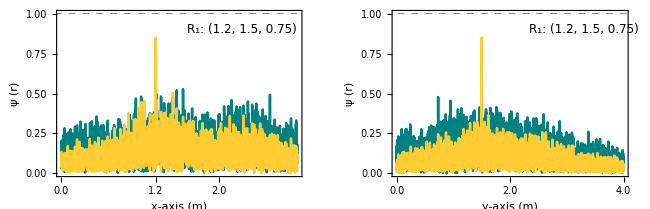

```mathematica
Show[GraphicsRow[{Show[crosSecPlotXUser1,crosSecPlotXUser1Pol],Show[crosSecPlotYUser1,crosSecPlotYUser1Pol]},Spacings->Scaled[0.1],ImageSize->650],Epilog->Inset[SwatchLegend[{RGBColor[0,0.5,0.5],RGBColor[1.,0.8,0.2]},{"No polarization","Polarization (greedy search)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},LegendLayout->"Row"],Scaled[{0.55,1.02}]  (*adjust position,e.g.,{0.5,1.02} for top-center*)],ImagePadding->{{0,0},{0,30}}]
```

```mathematica
crosSecPlotXUser2=radiationAlongX[2,userLocations1,dataPairMax];
crosSecPlotYUser2=radiationAlongY[2,userLocations1,dataPairMax];
```

```mathematica
crosSecPlotXUser2Pol=radiationAlongXPol[2,userLocations1,dataPairMax,sinrWithPolList[[1]]];
crosSecPlotYUser2Pol=radiationAlongYPol[2,userLocations1,dataPairMax,sinrWithPolList[[1]]];
```

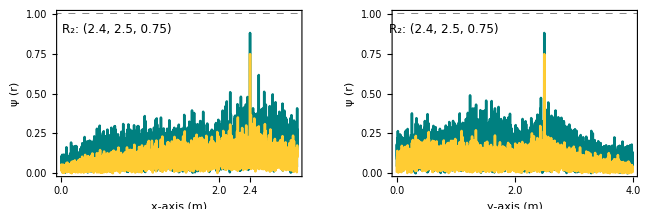

```mathematica
Show[GraphicsRow[{Show[crosSecPlotXUser2,crosSecPlotXUser2Pol],Show[crosSecPlotYUser2,crosSecPlotYUser2Pol]},Spacings->Scaled[0.1],ImageSize->650],Epilog->Inset[SwatchLegend[{RGBColor[0,0.5,0.5],RGBColor[1.,0.8,0.2]},{"No polarization","Polarization (greedy search)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},LegendLayout->"Row"],Scaled[{0.55,1.02}]  (*adjust position,e.g.,{0.5,1.02} for top-center*)],ImagePadding->{{0,0},{0,30}}]
```

```mathematica
crosSecPlotXUser3=radiationAlongX[3,userLocations1,dataPairMax];
crosSecPlotYUser3=radiationAlongY[3,userLocations1,dataPairMax];
```

```mathematica
crosSecPlotXUser3Pol=radiationAlongXPol[3,userLocations1,dataPairMax,sinrWithPolList[[1]]];
crosSecPlotYUser3Pol=radiationAlongYPol[3,userLocations1,dataPairMax,sinrWithPolList[[1]]];
```

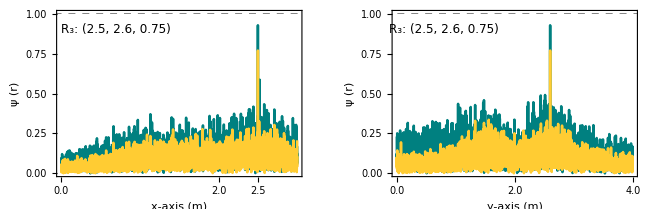

```mathematica
Show[GraphicsRow[{Show[crosSecPlotXUser3,crosSecPlotXUser3Pol],Show[crosSecPlotYUser3,crosSecPlotYUser3Pol]},Spacings->Scaled[0.1],ImageSize->650],Epilog->Inset[SwatchLegend[{RGBColor[0,0.5,0.5],RGBColor[1.,0.8,0.2]},{"No polarization","Polarization (greedy search)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},LegendLayout->"Row"],Scaled[{0.55,1.02}]  (*adjust position,e.g.,{0.5,1.02} for top-center*)],ImagePadding->{{0,0},{0,30}}]
```

```mathematica
crosSecPlotXUser4=radiationAlongX[4,userLocations1,dataPairMax];
crosSecPlotYUser4=radiationAlongY[4,userLocations1,dataPairMax];
```

```mathematica
crosSecPlotXUser4Pol=radiationAlongXPol[4,userLocations1,dataPairMax,sinrWithPolList[[1]]];
crosSecPlotYUser4Pol=radiationAlongYPol[4,userLocations1,dataPairMax,sinrWithPolList[[1]]];
```

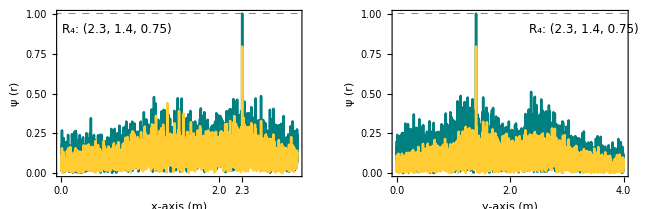

```mathematica
Show[GraphicsRow[{Show[crosSecPlotXUser4,crosSecPlotXUser4Pol],Show[crosSecPlotYUser4,crosSecPlotYUser4Pol]},Spacings->Scaled[0.1],ImageSize->650],Epilog->Inset[SwatchLegend[{RGBColor[0,0.5,0.5],RGBColor[1.,0.8,0.2]},{"No polarization","Polarization (greedy search)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},LegendLayout->"Row"],Scaled[{0.55,1.02}]  (*adjust position,e.g.,{0.5,1.02} for top-center*)],ImagePadding->{{0,0},{0,30}}]
```

```mathematica
crosSecPlotXUser5=radiationAlongX[5,userLocations1,dataPairMax];
crosSecPlotYUser5=radiationAlongY[5,userLocations1,dataPairMax];
```

```mathematica
crosSecPlotXUser5Pol=radiationAlongXPol[5,userLocations1,dataPairMax,sinrWithPolList[[1]]];
crosSecPlotYUser5Pol=radiationAlongYPol[5,userLocations1,dataPairMax,sinrWithPolList[[1]]];
```

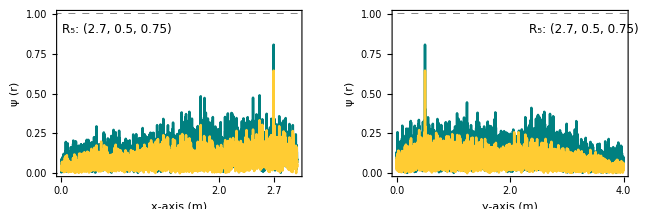

```mathematica
Show[GraphicsRow[{Show[crosSecPlotXUser5,crosSecPlotXUser5Pol],Show[crosSecPlotYUser5,crosSecPlotYUser5Pol]},Spacings->Scaled[0.1],ImageSize->650],Epilog->Inset[SwatchLegend[{RGBColor[0,0.5,0.5],RGBColor[1.,0.8,0.2]},{"No polarization","Polarization (greedy search)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},LegendLayout->"Row"],Scaled[{0.55,1.02}]  (*adjust position,e.g.,{0.5,1.02} for top-center*)],ImagePadding->{{0,0},{0,30}}]
```

```mathematica
crosSecPlotXUser6=radiationAlongX[6,userLocations1,dataPairMax];
crosSecPlotYUser6=radiationAlongY[6,userLocations1,dataPairMax];
```

```mathematica
crosSecPlotXUser6Pol=radiationAlongXPol[6,userLocations1,dataPairMax,sinrWithPolList[[1]]];
crosSecPlotYUser6Pol=radiationAlongYPol[6,userLocations1,dataPairMax,sinrWithPolList[[1]]];
```

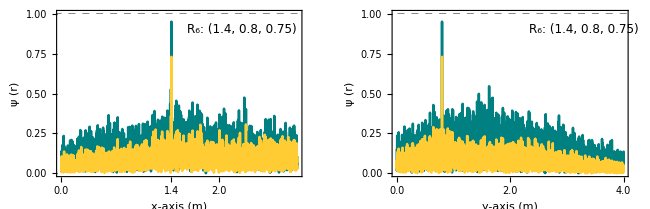

```mathematica
Show[GraphicsRow[{Show[crosSecPlotXUser6,crosSecPlotXUser6Pol],Show[crosSecPlotYUser6,crosSecPlotYUser6Pol]},Spacings->Scaled[0.1],ImageSize->650],Epilog->Inset[SwatchLegend[{RGBColor[0,0.5,0.5],RGBColor[1.,0.8,0.2]},{"No polarization","Polarization (greedy search)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},LegendLayout->"Row"],Scaled[{0.55,1.02}]  (*adjust position,e.g.,{0.5,1.02} for top-center*)],ImagePadding->{{0,0},{0,30}}]
```

Vector Plot generation

```mathematica
beamFocusingPatternPolVec[x_,y_,z_,focalPoints_,polVarsList_]:=Module[{arbitraryPoint,elementPoint,nx,ny,mx,my,clusterMidPoint,rt,rp,focalPointCount,subMatrixDim,r,c,m,n,assignedSubMatrices,beamFocusingPlanarCluster,rpI,deltaArrI,propagatedPolVec,proj},
arbitraryPoint={x,y,z};
elementPoint={xMiddle+(dis1/2*(2*nx-nx1-1)+Dis1/2*(2*mx-mx1-1)),yMiddle+(dis1/2*(2*ny-ny1-1)+Dis1/2*(2*my-my1-1)),zHeight};
clusterMidPoint={xMiddle+Dis1/2*(2*mx-mx1-1),yMiddle+Dis1/2*(2*my-my1-1),zHeight};
rt=EuclideanDistance[arbitraryPoint,clusterMidPoint];
rp=EuclideanDistance[arbitraryPoint,elementPoint];
focalPointCount=Length[focalPoints];
subMatrixDim=subdividingMatrix[nx1,ny1,focalPointCount];
r=subMatrixDim[[1]];
c=subMatrixDim[[2]];
beamFocusingPlanarCluster=0;
Do[
assignedSubMatrices=1;
For[m=1,m<=nx1,m+=r,{
(*Print[m];*)
For[n=1,n<=ny1,n+=c,{
(*Print[n];*)
If[assignedSubMatrices>focalPointCount,Break[],];
(*Print["user Location"]*);
(*Print[focalPoints[[assignedSubMatrices]]]*);
rpI=EuclideanDistance[focalPoints[[assignedSubMatrices]],elementPoint];
(*Print[rpI]*);
deltaArrI=rp-rpI;
(*Print[polVarsList[[mx,my,assignedSubMatrices]]]*);
propagatedPolVec=getPolVec[clusterMidPoint,arbitraryPoint,polVarsList[[assignedSubMatrices]]];

beamFocusingPlanarCluster+=propagatedPolVec*∑_(nx=m)^(m+r-1) ∑_(ny=n)^(n+c-1) (Cos[(2π)/λe*deltaArrI]*Exp[-ⅈ*(2π)/λd*deltaArrI])/rt;
(*Print["Done"]*);
assignedSubMatrices++;
}]
}];
,{mx,1,mx1},{my,1,my1}];
Re[Take[beamFocusingPlanarCluster,2]]
]
```

```mathematica
FindMaxEFieldVal[focalPoints_,polList_]:=Module[{plotDataPoints,magnitudes,posOfMax,maxLocation,maxVector,maxMag},
plotDataPoints=Flatten[ParallelTable[{{x,y},beamFocusingPatternPolVec[x,y,0.75,focalPoints,polList]},{x,0,xLength,0.1},{y,0,yLength,0.1}],1];
(*compute magnitudes of the vectors*)
magnitudes=Norm/@(plotDataPoints[[All,2]]);
(*find position of maximum magnitude*)
posOfMax=First[Ordering[magnitudes,-1]];
(*extract location and vector at this position*)
maxLocation=plotDataPoints[[posOfMax,1]];
maxVector=plotDataPoints[[posOfMax,2]];
maxMag=magnitudes[[posOfMax]];
(*show results*)
{maxLocation,maxVector,maxMag}
];
```

```mathematica
maxMag=FindMaxEFieldVal[userLocations1,sinrWithPolList[[1]]]
```

{{1.2,1.5},{95.7731,-18.3945},97.5236}

```mathematica
eFieldAtArbitraryPoint=beamFocusingPatternPolVec[x,y,0.75,userLocations1,sinrWithPolList[[1]]];
```

```mathematica
plotDataPoints=Flatten[ParallelTable[{{x,y},eFieldAtArbitraryPoint/maxMag[[3]]},{x,0,3,0.1},{y,0,4,0.1}],1];
```

```mathematica
(*Magnitude-colored vector plot generating function from {{x,y},{vx,vy}} data*)
ClearAll[AutoVectorPlot]
Options[AutoVectorPlot]={
"ArrowLenFrac"->1,(*longest arrow=this fraction of grid cell*)
"Arrowheads"->0.02,
"ArrowThickness"->0.005,
"SwapAxes"->False,(*set True if you display x<->y swapped*)
"ShowLegend"->True,
"ImageSize"->{300,300}
};

AutoVectorPlot[data:{{{_,_},{_,_}}..},userLocations_,OptionsPattern[]]:=Module[{points,vecs,mags,minMag,maxMag,cmap,posOfMax,maxLocation,gridx,gridy,dx,dy,ArrowLength,swap,ah,at,frLbl,arrows,tail,tip},
(*unpack+magnitudes*)
points=data[[All,1]];
vecs=data[[All,2]];
mags=Norm/@vecs;
{minMag,maxMag}=MinMax[mags];
cmap=ColorData["TemperatureMap"];
(* Find max vector location*)
posOfMax=First[Ordering[mags,-1]];
(*extract location and vector at this position*)
maxLocation=data[[posOfMax,1]];
(*grid spacing->choose a constant display length L for ALL arrows*)
gridx=Sort@DeleteDuplicates@points[[All,1]];
gridy=Sort@DeleteDuplicates@points[[All,2]];
dx=If[Length[gridx]>1,Min@Differences[gridx],1.0];
dy=If[Length[gridy]>1,Min@Differences[gridy],1.0];
ArrowLength=OptionValue["ArrowLenFrac"]*Min[dx,dy];
swap=TrueQ@OptionValue["SwapAxes"];
ah=OptionValue["Arrowheads"];
at=OptionValue["ArrowThickness"];
(*build arrows using MapThread*)
arrows=MapThread[Function[{p,vec,m},Module[{p2,v2,dir,col},
(*validate this item*)
If[!(VectorQ[p,NumericQ]&&Length[p]==2&&VectorQ[vec,NumericQ]&&Length[vec]==2&&NumericQ[m]),Nothing,(*skip malformed entries*)
p2=If[swap,Reverse[p],p];
v2=If[swap,Reverse[vec],vec];
If[m==0.,Return[Nothing]];(*skip true zero vector*)
dir=v2/m;(*unit direction*)
col=cmap@Rescale[m,{minMag,maxMag}];(*color by magnitude*)
tail=p2-0.5 ArrowLength*dir;(*center on point*)
tip=p2+0.5 ArrowLength *dir;
{col,Thickness[at],Arrowheads[ah],Arrow[{tail,tip}]}]]],{points,vecs,mags}];
Graphics[{arrows},Frame->True,Axes->False,AspectRatio->1,PlotRange->All,FrameLabel->{Style["x-axis",FontFamily->"Times New Roman",14,Black],Style["y-axis",FontFamily->"Times New Roman",14,Black]},LabelStyle->{FontFamily->"Times New Roman",12,Black},PlotLabel->Style["Normalized E-field at Receiver Plane",FontFamily->"Times New Roman",FontSize->16,Black,Bold],ImageSize->{500,500},ImagePadding->{{40,80},{38,10}},PlotRangeClipping->False,Epilog->{Text[Style[Row[{"R_1 (",NumberForm[userLocations[[1,1]],{Infinity,1}],",",NumberForm[userLocations[[1,2]],{Infinity,1}],")"}],FontFamily->"Times New Roman",FontSize->14,Black,Bold],{userLocations[[1,1]],userLocations[[1,2]]+0.1}],Text[Style[Row[{"R_2 (",NumberForm[userLocations[[2,1]],{Infinity,1}],",",NumberForm[userLocations[[2,2]],{Infinity,1}],")"}],FontFamily->"Times New Roman",FontSize->14,Black,Bold],{userLocations[[2,1]],userLocations[[2,2]]-0.2}],Text[Style[Row[{"R_3 (",NumberForm[userLocations[[3,1]],{Infinity,1}],",",NumberForm[userLocations[[3,2]],{Infinity,1}],")"}],FontFamily->"Times New Roman",FontSize->14,Black,Bold],{userLocations[[3,1]],userLocations[[3,2]]+0.15}],Text[Style[Row[{"R_4 (",NumberForm[userLocations[[4,1]],{Infinity,1}],",",NumberForm[userLocations[[4,2]],{Infinity,1}],")"}],FontFamily->"Times New Roman",FontSize->14,Black,Bold],{userLocations[[4,1]],userLocations[[4,2]]+0.1}],Text[Style[Row[{"R_5 (",NumberForm[userLocations[[5,1]],{Infinity,1}],",",NumberForm[userLocations[[5,2]],{Infinity,1}],")"}],FontFamily->"Times New Roman",FontSize->14,Black,Bold],{userLocations[[5,1]],userLocations[[5,2]]+0.1}],Text[Style[Row[{"R_6 (",NumberForm[userLocations[[6,1]],{Infinity,1}],",",NumberForm[userLocations[[6,2]],{Infinity,1}],")"}],FontFamily->"Times New Roman",FontSize->14,Black,Bold],{userLocations[[6,1]],userLocations[[6,2]]+0.1}],Inset[BarLegend[{cmap,{0,1}},LabelStyle->{FontFamily->"Times New Roman",14,Black},LegendMargins->8,LegendMarkerSize->{18,350}],Scaled[{1.1,0.5}]]}]];
```

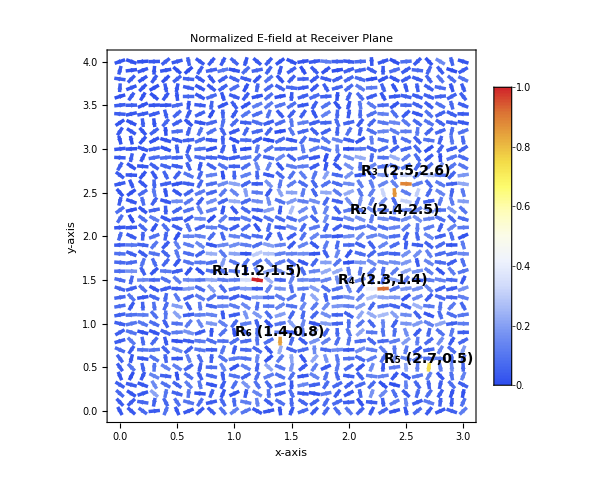

```mathematica
eFieldPlot=AutoVectorPlot[plotDataPoints,Drop[#,-1]&/@userLocations1]
```

Comparison of exhaustive Search and greedy Search (Runtime vs Q, and means SINR vs Q)

```mathematica
(*Generate random locations*)
```

```mathematica
(*2471*)
```

```mathematica
genLayout[Q_]:=BlockRandom[SeedRandom[1238,Method->"MersenneTwister"];(*fixed seed*)Table[{Round[RandomReal[{0,3}],0.1],Round[RandomReal[{0,4}],0.1],0.75},{Q}]];
```

```mathematica
(*Function to run two algorithms*)
```

```mathematica
runAlgo[Q_,noiseVar_,restartCount_]:=Module[{userLocations,subClusDim,sinrUnPol,exhaustAlgo,exhaustTime,exhaustMean,greedyAlgo,greedyTiming,greedyMean},
userLocations=genLayout[Q];
Print[userLocations];
subClusDim=subdividingMatrix[nx1,ny1,Length[userLocations]];
sinrUnPol=sinrCal[userLocations,subClusDim];
exhaustAlgo=Table[AbsoluteTiming[sinrCalPol[userLocations,sinrUnPol,subClusDim]],5];
exhaustTime=Mean[exhaustAlgo[[All,1]]];
exhaustMean=Mean[exhaustAlgo[[All,2]][[All,3]]];
greedyAlgo=Table[AbsoluteTiming[greedyHV[subClusDim,userLocations,noiseVar,sinrUnPol,restartCount]],5];
greedyTiming=Mean[greedyAlgo[[All,1]]];
greedyMean=Mean[greedyAlgo[[All,2]][[All,3]]];
{Q,exhaustTime,exhaustMean,greedyTiming,greedyMean,Mean[sinrUnPol]}
]
```

```mathematica
runtimevariables=Table[runAlgo[q,10,5],{q,1,10}]
```

{{0.,0.3,0.75}}

{{0.,0.3,0.75},{1.3,2.1,0.75}}

{{0.,0.3,0.75},{1.3,2.1,0.75},{0.1,3.5,0.75}}

{{0.,0.3,0.75},{1.3,2.1,0.75},{0.1,3.5,0.75},{2.2,2.5,0.75}}

{{0.,0.3,0.75},{1.3,2.1,0.75},{0.1,3.5,0.75},{2.2,2.5,0.75},{1.1,3.2,0.75}}

{{0.,0.3,0.75},{1.3,2.1,0.75},{0.1,3.5,0.75},{2.2,2.5,0.75},{1.1,3.2,0.75},{1.7,2.3,0.75}}

{{0.,0.3,0.75},{1.3,2.1,0.75},{0.1,3.5,0.75},{2.2,2.5,0.75},{1.1,3.2,0.75},{1.7,2.3,0.75},{2.2,2.2,0.75}}

{{0.,0.3,0.75},{1.3,2.1,0.75},{0.1,3.5,0.75},{2.2,2.5,0.75},{1.1,3.2,0.75},{1.7,2.3,0.75},{2.2,2.2,0.75},{0.3,2.5,0.75}}

{{0.,0.3,0.75},{1.3,2.1,0.75},{0.1,3.5,0.75},{2.2,2.5,0.75},{1.1,3.2,0.75},{1.7,2.3,0.75},{2.2,2.2,0.75},{0.3,2.5,0.75},{0.7,0.3,0.75}}

{{0.,0.3,0.75},{1.3,2.1,0.75},{0.1,3.5,0.75},{2.2,2.5,0.75},{1.1,3.2,0.75},{1.7,2.3,0.75},{2.2,2.2,0.75},{0.3,2.5,0.75},{0.7,0.3,0.75},{1.5,2.2,0.75}}

{{1,0.00302702,42.291,0.0225921,42.291,44.4074},{2,0.185878,37.5281,0.965906,37.5281,35.6129},{3,0.733859,33.1396,2.56986,33.1301,30.238},{4,2.61597,28.9255,6.05954,28.6831,22.2319},{5,5.39612,26.2747,8.81863,25.781,20.1641},{6,33.755,23.9563,44.3726,23.9563,19.0269},{7,68.2189,21.1299,39.607,21.1299,14.0366},{8,150.311,19.5818,25.8325,19.5818,14.4102},{9,238.26,20.1224,68.0224,19.0082,14.8524},{10,435.735,19.7986,57.5952,19.0057,16.4013}}

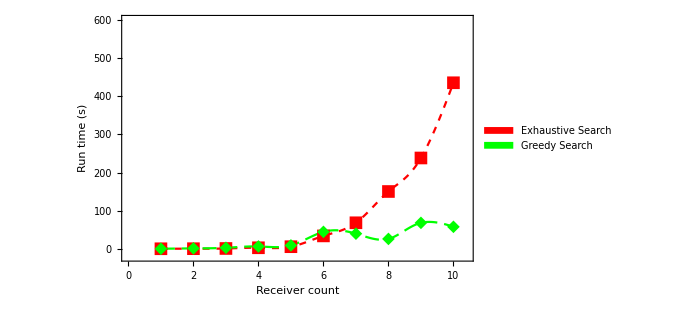

```mathematica
ListLinePlot[{runtimevariables[[All,2]],runtimevariables[[All,4]]},PlotStyle->{{Dashing[{0.01,0.01}],Red},{Dashing[{0.02,0.01}],Green}},InterpolationOrder->3,PlotMarkers->{Style["■",13],Style["◆",13]},PlotLegends->Placed[SwatchLegend[{"Exhaustive Search","Greedy Search"},LabelStyle->{FontFamily->"Times New Roman"}],{0.2,0.8}],PlotRange->{{0,10.4},{-20,600}},ImageSize->500,BaseStyle->{FontFamily->"Times New Roman",FontSize->14},Frame->True,FrameLabel->{(*use frame labels instead of axes labels*)Style["Receiver count",FontFamily->"Times New Roman",FontSize->14],Style["Run time (s)",FontFamily->"Times New Roman",FontSize->14]},ImagePadding->{{60,10},{40,10}}]
```

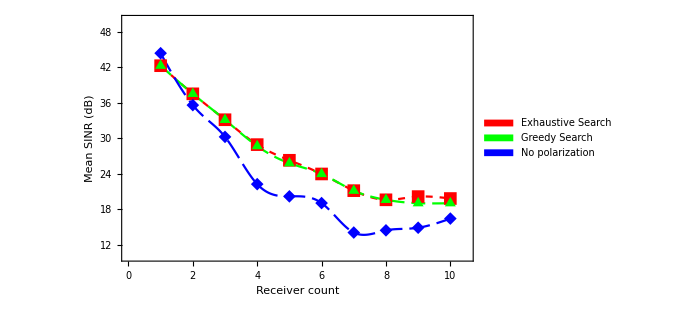

```mathematica
ListLinePlot[{runtimevariables[[All,3]],runtimevariables[[All,5]],runtimevariables[[All,6]]},PlotStyle->{{Dashing[{0.01,0.01}],Red},{Dashing[{0.02,0.01}],Green},{Dashing[{0.03,0.01}],Blue}},InterpolationOrder->3,PlotMarkers->{Style["■",13],Style["▲",13],Style["◆",13]},PlotLegends->Placed[SwatchLegend[{"Exhaustive Search","Greedy Search","No polarization"},LabelStyle->{FontFamily->"Times New Roman"}],{0.8,0.8}],PlotRange->{{0,10.5},{10,50}},ImageSize->500,BaseStyle->{FontFamily->"Times New Roman",FontSize->14},Frame->True,FrameLabel->{(*use frame labels instead of axes labels*)Style["Receiver count",FontFamily->"Times New Roman",FontSize->14],Style["Mean SINR (dB)",FontFamily->"Times New Roman",FontSize->14]},ImagePadding->{{40,10},{40,10}}]
```